```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*ICs - Initial Conditions *) (* Error while cosntraining u *)


CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},xState={x,xdot,θ,θdot};x2dot=(u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2);θ2dot=(-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]))/(1-A Cos[θ]^2);fx={xdot,x2dot,θdot,θ2dot};L=u^2/2;Af=fxxState;Bf=D[fx, u];Q=LxStatexState;Mf=D[L, u]xState;R=D[L, {u,2}];S0={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};RHS[t_]:=IdentityMatrix[4]+Transpose[Af].S[t]+S[t].Af-KroneckerProduct[S[t].Bf,Transpose[Bf].S[t]]/.{x->x1a[τ-t],xdot->xdot1a[τ-t],θ->θ1a[τ-t],θdot->θdot1a[τ-t],u->u1a[τ-t]};sol2=S/.NDSolve[{S'[t]==RHS[t],S[0]==S0},S,{t,0,τ}];S=sol2⟦1⟧]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]

ffCartPendulum[ICs_,systemData_]:=
Module[{n,τ,τ1,A,time1,time2,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
{n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ} = systemData;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;


uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;


];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[time_] := CalculateGains[xff,xdotff,θff,θdotff,uff,time,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]

ffCartPendulumTimed[ICs_,systemData_]:=
Module[{n,τ,τ1,A,time1,time2,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
{n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,initGuess,maxJ} = systemData;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

{time1,froot}=Timing[FindRoot[eqns,sv,MaxIterations->maxIter]];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;

Print["Error First Guess = ",error];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;

Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];

];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{time2,S} = Timing[CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A]];
K[time_] := CalculateGains[xff,xdotff,θff,θdotff,uff,time,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K,time1,time2}]


testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]



testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]

testWithFBClipped[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:= Clip[uff[t]+ufb[t],{-uBound,uBound}];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=Clip[uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];


J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
Energy[{x1_,x2_,θ1_,θ2_,A_}] := 1/2*x2^2 + 1/2*A*θ2^2 + A*Cos[θ1]*x2*θ2 - A*Cos[θ1];
```

Remove::rmnsm: There are no symbols matching "Global`*".

Initial Energy = -0.0267107

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$16509 near {t$16509} = {0.114848}. NIntegrate obtained 22.609 and 0.000807803 for the integral and error estimates.

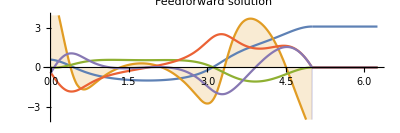
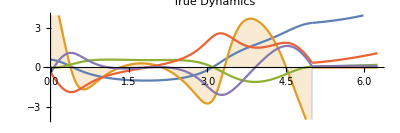
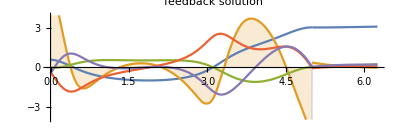
-Graphics- | -Graphics- | -Graphics-

Computation Time = 0.90625

```mathematica
n=30;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 5;maxJ = uMax^2*τ;InitGuess = {0,0,0,0};
xdotMin = -2;xdotMax = 2;θMin = -π;θMax = π;θdotMin = -2;θdotMax = 2;
xdotInit = RandomReal[{xdotMin,xdotMax}];θInit = RandomReal[{θMin,θMax}];θdotInit = RandomReal[{θdotMin,θdotMax}];ICs = {0,xdotInit,θInit,θdotInit};
ICs ={0,0.9529541584443537,1.7457414225874786,0.9652436212686677};
ICs = ICData[[1]];
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
Print["Initial Energy = ", EInitial];
systemData = {n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ} ;

{time,{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}}=Timing[ffCartPendulum[ICs,systemData]]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J} = testSwingUp[ICs,τ,τ1,u1a,A];
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1b=Plot[{θ1b[t],u1b[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"True Dynamics ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"feedback solution ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1b,p1c}}]
Print["Computation Time = ", time];
```

### Define Computation Time function

```mathematica
n=30;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 20;maxJ = 2^2*τ;InitGuess = {0,0,0,0};
xdotMin = -2;xdotMax = 2;θMin = -π;θMax = π;θdotMin = -2;θdotMax = 2;
systemData = {n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ} ;
ComputationTime[ICs_] := Module[{time},
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
{time,{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}}=Quiet[RepeatedTiming[ffCartPendulum[ICs,systemData]]]; 
time
]
ICData = Import["ICDataComputation20.mx"];
EData = Import["EDataComputation20.mx"];
```

```mathematica
ComputationTime[ICData[[1]]]
```

0.874253

```mathematica
(*ICData = Table[
xdotInit = RandomReal[{xdotMin,xdotMax}];θInit = RandomReal[{θMin,θMax}];θdotInit = RandomReal[{θdotMin,θdotMax}];
{0,xdotInit,θInit,θdotInit},
{i,1,numberTests}];*)
ICData
EData
```

{{0,-0.442495,0.605262,-0.364812},{0,-1.11903,-2.21388,1.7311},{0,-1.77545,-0.799806,-1.65722},{0,-0.716047,2.63917,0.171617},{0,0.808789,-0.379552,0.333731},{0,-0.113716,-0.133059,0.452483},{0,1.3249,-2.01376,0.826175},{0,0.112189,-0.662448,-1.391},{0,1.65138,-1.43999,-0.427961},{0,0.106668,-0.523286,1.96092},{0,-0.481794,-2.51711,0.157573},{0,1.22129,-2.18835,0.82422},{0,1.28214,-2.15401,1.20565},{0,-0.571285,0.130894,-0.453014},{0,1.18198,0.550235,0.47},{0,1.07068,-1.57722,-1.63188},{0,1.2006,-2.02498,-1.15245},{0,-1.03112,-1.33483,-1.25604},{0,-1.34733,-1.08826,1.27634},{0,-1.96186,-0.181651,-0.575824},{0,-0.0260151,-1.64763,-0.214132},{0,0.764322,-1.89452,0.216266},{0,0.33616,-1.12835,-1.17905},{0,1.12069,-2.60762,0.801591},{0,1.74021,2.3823,1.3284},{0,-1.19048,-1.07296,1.55175},{0,1.02866,1.93763,1.77935},{0,-0.421943,2.58814,0.903611},{0,-0.0302922,1.75646,1.24408},{0,1.41683,0.785186,-1.27777},{0,-0.804409,1.72206,1.16616},{0,-0.466595,-2.56643,1.6098},{0,-0.507026,0.223631,-1.65738},{0,1.41857,2.29382,-1.59222},{0,-0.414386,2.1543,0.264887},{0,0.519566,2.24368,0.298204},{0,0.468829,3.05678,-1.44083},{0,1.07279,0.201323,-0.0438603},{0,1.45149,1.50282,1.1472},{0,-0.161646,-2.24272,1.56239},{0,-1.93905,-2.64771,-1.18886},{0,-0.229059,1.58882,1.04383},{0,-1.83903,0.167039,1.26379},{0,1.83686,2.82913,-1.54332},{0,1.62621,-0.140321,-0.904589},{0,0.284573,1.9009,1.36679},{0,0.396096,1.36054,0.228754},{0,1.46556,-1.15597,-1.82268},{0,1.9334,0.0527347,0.0522149},{0,1.74546,0.338323,-0.620041},{0,0.94161,-0.0413514,1.08166},{0,0.994583,-1.09904,-1.20655},{0,1.18197,2.09849,1.34838},{0,-0.0563296,0.835199,-1.31943},{0,0.86026,2.69824,0.763766},{0,-1.40018,1.75386,-0.350543},{0,-1.80656,1.08905,0.714857},{0,1.91185,-3.10936,-1.97502},{0,-0.322869,-2.32187,1.15593},{0,-0.0582253,2.43187,0.446207},{0,-0.461735,-3.11083,-1.94066},{0,-0.415697,0.677934,0.915084},{0,1.67904,-2.78537,0.0189325},{0,-1.23946,0.52134,-1.55038},{0,1.46178,1.23433,-0.742644},{0,1.32014,-3.0027,-0.305629},{0,1.10375,0.323125,-0.8636},{0,1.11879,3.01271,-0.784057},{0,0.277621,1.56983,-1.812},{0,-1.54848,-1.90083,1.40035},{0,1.7301,-2.95681,-0.891417},{0,-0.59687,-0.68798,1.6397},{0,-0.373833,-0.360979,0.0384947},{0,1.11637,-0.799424,-0.880469},{0,-1.15111,-1.70477,0.468491},{0,-0.32232,2.90766,-0.136466},{0,-0.204727,0.241,0.524967},{0,-0.542854,1.59762,0.036314},{0,-0.389391,-1.26521,-1.89481},{0,1.4791,-1.68965,-0.141322},{0,0.22701,-3.0697,-1.85743},{0,1.15099,-1.42823,0.188269},{0,0.376878,-1.25573,1.93571},{0,0.438914,-0.47471,-1.29244},{0,1.26833,1.97801,1.22745},{0,0.503535,-1.29319,-0.487559},{0,0.837068,-1.1147,0.188074},{0,-1.02999,-1.48102,-1.97307},{0,1.37458,1.19075,1.34743},{0,1.20649,1.9971,0.40112},{0,0.124397,2.77277,1.86648},{0,-0.177802,0.193062,0.486354},{0,1.96305,2.17268,1.18746},{0,-0.673487,0.467805,-0.907596},{0,0.0659282,1.37257,0.640491},{0,0.972964,1.57389,-1.86145},{0,1.29068,2.51095,-1.26457},{0,0.0410663,-3.14145,-0.270232},{0,1.16004,0.557325,-0.763725},{0,-0.0236634,2.00731,-1.89346},{0,-1.93813,-2.74996,1.12589},{0,-1.59911,2.79152,1.9661},{0,1.21669,0.532392,0.0268653},{0,0.563073,1.42146,0.978124},{0,1.57379,2.01397,0.649465},{0,-1.73468,-0.409001,1.07221},{0,-0.545613,-2.47553,1.33858},{0,0.36531,2.14385,-0.0314718},{0,1.06964,2.07545,-1.54419},{0,1.67153,-0.79966,1.41538},{0,-0.700915,2.95868,-1.72901},{0,1.65251,-2.24098,0.390857},{0,-1.60054,1.68778,1.74518},{0,1.11682,-1.33045,-1.51838},{0,-1.32099,2.261,1.78436},{0,1.56648,-2.65254,-0.227298},{0,-0.196867,-0.733974,0.293393},{0,-1.28465,-0.896772,-1.86203},{0,0.5317,-0.688199,0.0424878},{0,-1.665,0.974569,1.41572},{0,-1.74844,-0.738101,-0.238376},{0,-0.0854191,-0.795332,-1.4066},{0,-0.352132,-0.884957,0.207843},{0,-0.604527,2.84763,-1.73223},{0,0.440314,0.464401,-0.566971},{0,0.549875,1.72279,1.82008},{0,-0.0852747,-0.343854,0.760292},{0,0.0871327,-1.11973,1.99376},{0,1.56521,0.095867,1.6637},{0,0.324583,2.59882,-1.54189},{0,-1.17645,-0.394487,-0.262494},{0,1.87908,1.32012,-1.97416},{0,0.705521,0.237783,-1.25761},{0,0.141345,2.28971,1.05293},{0,0.716391,1.8972,1.35035},{0,-1.25733,0.519407,0.449241},{0,1.64725,-1.57229,-1.06536},{0,-0.0199518,-2.5434,-0.665624},{0,1.82949,-0.254018,-0.780621},{0,-0.366504,0.581274,1.38453},{0,-0.810498,2.35934,0.502631},{0,0.584348,3.03935,-0.773647},{0,-1.91454,1.60553,1.74311},{0,-1.88851,-0.0901817,-0.673328},{0,-1.42722,-2.03113,-0.567687},{0,0.0960397,-2.21034,-0.463016},{0,1.50072,1.88893,1.70586},{0,-0.851532,2.95906,-0.545981},{0,-0.386111,-1.78997,-1.49979},{0,1.27075,-2.52054,-1.30153},{0,1.93741,1.60372,-1.52363},{0,0.95229,0.521779,-1.68621},{0,1.51377,0.945932,-0.650621},{0,1.34041,2.34939,-1.5191},{0,-1.28662,-0.842249,-0.0707028},{0,-0.477039,-2.47579,-1.13184},{0,0.739177,2.1409,0.268093},{0,-1.71582,1.04581,1.14519},{0,1.19914,-2.23553,-0.702026},{0,-1.71826,-0.439465,-1.83133},{0,1.05961,2.89724,-0.969699},{0,0.221066,0.837771,1.6262},{0,1.37626,1.91489,1.82572},{0,-1.95509,0.362807,1.64073},{0,1.57386,2.8262,-1.54718},{0,1.56654,1.50125,-1.27804},{0,-1.30462,0.461738,-1.44537},{0,0.520771,-1.73828,-1.24577},{0,-0.916173,1.4169,-1.65099},{0,0.439102,-0.547954,-0.891864},{0,0.111929,0.743857,0.955712},{0,-1.96439,0.426676,-1.6673},{0,-1.52982,2.06668,1.68345},{0,-1.30014,2.1837,-0.163524},{0,-1.15394,-0.940231,0.091836},{0,-0.157022,0.119174,-0.666163},{0,0.89204,0.800392,-0.982356},{0,0.55195,-1.87974,0.397935},{0,1.23322,1.37971,0.798055},{0,-1.39457,-2.61327,1.65523},{0,-0.0123778,0.410761,-0.42593},{0,-0.0231721,-2.83158,1.2809},{0,1.19091,-2.82701,1.04025},{0,-1.89526,0.0550934,-1.11603},{0,-1.51786,-2.92811,0.777523},{0,0.860408,3.09154,1.9335},{0,-0.837895,0.896279,1.30841},{0,-1.7171,2.79718,1.48527},{0,-0.511557,1.20128,-1.1189},{0,-0.343645,1.18385,1.36322},{0,-0.138767,-1.57079,-1.57722},{0,-0.63717,1.94361,0.648066},{0,-0.368418,-1.74715,-0.759664},{0,0.573644,-2.48762,-0.702498},{0,-1.5754,-1.48014,-1.95346},{0,1.12807,-0.0650244,-1.05358},{0,0.222117,-0.716457,0.117776},{0,-0.743687,-2.72321,1.96279},{0,1.31725,-2.53797,-1.41447},{0,1.90058,-1.57112,1.59354}}

{-0.0267107,1.27804,2.12145,0.456131,0.202582,-0.181492,0.937832,0.0174727,1.33733,0.253209,0.293116,0.812943,0.907179,0.0367336,0.644854,0.843012,1.0627,0.703168,0.818161,1.98312,0.0201903,0.349874,0.0759484,0.709731,1.50035,0.677474,0.786115,0.405683,0.193544,0.769439,0.51794,0.661875,0.372091,1.69091,0.21516,0.249203,0.651394,0.370451,1.19405,0.413114,1.79144,0.139659,1.19516,2.65506,0.914752,0.266917,0.0457181,1.11023,1.68974,1.16891,0.564009,0.440213,0.820547,0.0514451,0.490318,1.01108,1.4706,3.17235,0.373163,0.177255,0.503992,-0.0448903,1.5911,1.16834,0.985845,1.15872,0.31329,1.05965,0.366581,1.60035,2.07588,0.14127,-0.119779,0.424195,0.725592,0.239802,-0.166578,0.152946,0.419066,1.12454,0.654369,0.643677,0.428954,-0.0154312,0.910885,0.0822775,0.279657,0.938247,1.18952,0.786575,0.499348,-0.173797,1.91707,0.239769,0.00547393,0.821568,1.41802,0.210365,0.411058,0.439569,2.59317,2.44367,0.573553,0.24083,1.2787,1.09471,0.600126,0.176511,1.06694,1.78773,0.502918,1.42467,1.67398,0.725849,1.61839,1.47151,-0.129095,1.34564,-0.00945546,1.20951,1.44791,0.0783136,-0.0696166,0.473757,-0.0943752,0.482424,-0.13906,0.329267,1.82107,0.547385,0.571285,1.92156,0.040205,0.232966,0.441046,0.538923,1.47104,0.207581,1.26441,0.0068838,0.553376,0.519484,2.1667,1.88268,1.06756,0.150724,1.31949,0.497601,0.317781,1.40847,2.13494,0.285954,0.955859,1.55557,0.707145,0.314251,0.366932,1.30596,0.99548,2.20013,1.04888,0.203174,1.17831,1.39362,2.13101,1.34864,1.21852,0.345767,0.707978,-0.0616276,-0.0338267,2.62166,1.79381,0.93845,0.536214,-0.121104,0.233029,0.215613,0.823505,1.81784,-0.164179,0.360459,0.771926,2.14324,1.63855,0.611439,0.26039,2.36319,0.22515,0.134052,0.258391,0.34792,0.150842,0.436586,1.66015,0.310494,-0.120827,1.1113,1.53909,2.0599}

### Use the above 200 ICData points for all simulations

```mathematica
numberTests = 200;
n=30;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 20;maxJ = 2^2*τ;InitGuess = {0,0,0,0};
xdotMin = -2;xdotMax = 2;θMin = -π;θMax = π;θdotMin = -2;θdotMax = 2;
systemData = {n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ} ;

TimingData = ParallelTable[ComputationTime[ICData[[i]]],{i,1,numberTests}];
EData = Table[ Energy[Join[Table[ICData[[i]][[j]],{j,1,4}],{A}]],{i,1,numberTests}];

Export["TimingDataComputation30.mx",TimingData];
Export["ICDataComputation30.mx",ICData];
Export["EDataComputation30.mx",EData];
```

```mathematica
TimingData
ICData
```

{12.5362,0.940294,1.0792,0.878349,0.959985,1.04219,1.00886,1.20691,1.04444,0.948802,0.936446,0.953206,1.03958,11.6224,0.913742,13.9967,13.807,1.00884,1.03553,1.1554,1.04665,0.883834,1.19662,1.01491,2.11895,1.01086,4.56195,0.962611,0.897908,1.09388,0.990069,0.996781,1.16298,1.07136,12.1226,13.1538,12.8241,1.01855,12.5616,0.933471,5.06185,13.9801,7.08397,1.07705,0.910837,0.827237,1.04823,1.09554,1.01353,1.01138,5.48872,1.18468,0.987173,12.8926,2.99088,12.5253,12.0321,13.7607,0.936473,2.12154,13.9556,1.03353,1.12324,1.13911,0.981387,13.745,0.975014,12.2857,12.9281,0.916551,13.425,0.93069,1.09496,1.01144,0.921965,0.874295,1.08678,1.07975,1.30957,1.10904,13.1418,0.942762,3.25942,1.0196,1.00456,0.932242,1.003,1.64728,11.6787,11.9267,13.1105,1.08808,13.621,14.71,12.3034,0.988108,1.59319,5.4988,1.04817,12.9686,0.910832,13.412,0.995043,13.3856,12.487,3.0252,0.948308,12.3101,1.08045,1.05391,454.971,0.754495,10.1529,0.849638,10.1966,9.76356,1.00447,2.43423,1.01629,0.951779,1.01395,1.05958,1.79451,12.2838,1.10828,1.46744,0.94389,0.903005,0.951853,1.08241,1.01521,1.10354,1.01889,0.912646,1.01036,11.802,13.7023,1.83547,0.994493,1.75571,0.894964,12.9158,13.5998,1.22169,1.07689,1.20103,5.0506,3.262,3.1563,13.5977,2.98148,1.08007,1.00457,1.07898,1.08418,1.70785,12.2958,13.7061,13.6453,1.12945,14.3796,0.858206,3.18194,0.924767,1.17376,2.18413,1.14983,12.6976,13.0641,1.0439,1.07324,1.01537,13.1744,11.6419,1.01212,1.03901,1.1314,0.918027,12.0999,0.986106,1.12328,0.921944,0.952577,1.16831,1.0001,414.517,1.61099,10.0135,12.4017,12.7201,1.04904,11.1282,0.957866,1.57742,1.66118,0.889567,0.902171,0.875797,13.1987,0.924145}

{{0,-0.442495,0.605262,-0.364812},{0,-1.11903,-2.21388,1.7311},{0,-1.77545,-0.799806,-1.65722},{0,-0.716047,2.63917,0.171617},{0,0.808789,-0.379552,0.333731},{0,-0.113716,-0.133059,0.452483},{0,1.3249,-2.01376,0.826175},{0,0.112189,-0.662448,-1.391},{0,1.65138,-1.43999,-0.427961},{0,0.106668,-0.523286,1.96092},{0,-0.481794,-2.51711,0.157573},{0,1.22129,-2.18835,0.82422},{0,1.28214,-2.15401,1.20565},{0,-0.571285,0.130894,-0.453014},{0,1.18198,0.550235,0.47},{0,1.07068,-1.57722,-1.63188},{0,1.2006,-2.02498,-1.15245},{0,-1.03112,-1.33483,-1.25604},{0,-1.34733,-1.08826,1.27634},{0,-1.96186,-0.181651,-0.575824},{0,-0.0260151,-1.64763,-0.214132},{0,0.764322,-1.89452,0.216266},{0,0.33616,-1.12835,-1.17905},{0,1.12069,-2.60762,0.801591},{0,1.74021,2.3823,1.3284},{0,-1.19048,-1.07296,1.55175},{0,1.02866,1.93763,1.77935},{0,-0.421943,2.58814,0.903611},{0,-0.0302922,1.75646,1.24408},{0,1.41683,0.785186,-1.27777},{0,-0.804409,1.72206,1.16616},{0,-0.466595,-2.56643,1.6098},{0,-0.507026,0.223631,-1.65738},{0,1.41857,2.29382,-1.59222},{0,-0.414386,2.1543,0.264887},{0,0.519566,2.24368,0.298204},{0,0.468829,3.05678,-1.44083},{0,1.07279,0.201323,-0.0438603},{0,1.45149,1.50282,1.1472},{0,-0.161646,-2.24272,1.56239},{0,-1.93905,-2.64771,-1.18886},{0,-0.229059,1.58882,1.04383},{0,-1.83903,0.167039,1.26379},{0,1.83686,2.82913,-1.54332},{0,1.62621,-0.140321,-0.904589},{0,0.284573,1.9009,1.36679},{0,0.396096,1.36054,0.228754},{0,1.46556,-1.15597,-1.82268},{0,1.9334,0.0527347,0.0522149},{0,1.74546,0.338323,-0.620041},{0,0.94161,-0.0413514,1.08166},{0,0.994583,-1.09904,-1.20655},{0,1.18197,2.09849,1.34838},{0,-0.0563296,0.835199,-1.31943},{0,0.86026,2.69824,0.763766},{0,-1.40018,1.75386,-0.350543},{0,-1.80656,1.08905,0.714857},{0,1.91185,-3.10936,-1.97502},{0,-0.322869,-2.32187,1.15593},{0,-0.0582253,2.43187,0.446207},{0,-0.461735,-3.11083,-1.94066},{0,-0.415697,0.677934,0.915084},{0,1.67904,-2.78537,0.0189325},{0,-1.23946,0.52134,-1.55038},{0,1.46178,1.23433,-0.742644},{0,1.32014,-3.0027,-0.305629},{0,1.10375,0.323125,-0.8636},{0,1.11879,3.01271,-0.784057},{0,0.277621,1.56983,-1.812},{0,-1.54848,-1.90083,1.40035},{0,1.7301,-2.95681,-0.891417},{0,-0.59687,-0.68798,1.6397},{0,-0.373833,-0.360979,0.0384947},{0,1.11637,-0.799424,-0.880469},{0,-1.15111,-1.70477,0.468491},{0,-0.32232,2.90766,-0.136466},{0,-0.204727,0.241,0.524967},{0,-0.542854,1.59762,0.036314},{0,-0.389391,-1.26521,-1.89481},{0,1.4791,-1.68965,-0.141322},{0,0.22701,-3.0697,-1.85743},{0,1.15099,-1.42823,0.188269},{0,0.376878,-1.25573,1.93571},{0,0.438914,-0.47471,-1.29244},{0,1.26833,1.97801,1.22745},{0,0.503535,-1.29319,-0.487559},{0,0.837068,-1.1147,0.188074},{0,-1.02999,-1.48102,-1.97307},{0,1.37458,1.19075,1.34743},{0,1.20649,1.9971,0.40112},{0,0.124397,2.77277,1.86648},{0,-0.177802,0.193062,0.486354},{0,1.96305,2.17268,1.18746},{0,-0.673487,0.467805,-0.907596},{0,0.0659282,1.37257,0.640491},{0,0.972964,1.57389,-1.86145},{0,1.29068,2.51095,-1.26457},{0,0.0410663,-3.14145,-0.270232},{0,1.16004,0.557325,-0.763725},{0,-0.0236634,2.00731,-1.89346},{0,-1.93813,-2.74996,1.12589},{0,-1.59911,2.79152,1.9661},{0,1.21669,0.532392,0.0268653},{0,0.563073,1.42146,0.978124},{0,1.57379,2.01397,0.649465},{0,-1.73468,-0.409001,1.07221},{0,-0.545613,-2.47553,1.33858},{0,0.36531,2.14385,-0.0314718},{0,1.06964,2.07545,-1.54419},{0,1.67153,-0.79966,1.41538},{0,-0.700915,2.95868,-1.72901},{0,1.65251,-2.24098,0.390857},{0,-1.60054,1.68778,1.74518},{0,1.11682,-1.33045,-1.51838},{0,-1.32099,2.261,1.78436},{0,1.56648,-2.65254,-0.227298},{0,-0.196867,-0.733974,0.293393},{0,-1.28465,-0.896772,-1.86203},{0,0.5317,-0.688199,0.0424878},{0,-1.665,0.974569,1.41572},{0,-1.74844,-0.738101,-0.238376},{0,-0.0854191,-0.795332,-1.4066},{0,-0.352132,-0.884957,0.207843},{0,-0.604527,2.84763,-1.73223},{0,0.440314,0.464401,-0.566971},{0,0.549875,1.72279,1.82008},{0,-0.0852747,-0.343854,0.760292},{0,0.0871327,-1.11973,1.99376},{0,1.56521,0.095867,1.6637},{0,0.324583,2.59882,-1.54189},{0,-1.17645,-0.394487,-0.262494},{0,1.87908,1.32012,-1.97416},{0,0.705521,0.237783,-1.25761},{0,0.141345,2.28971,1.05293},{0,0.716391,1.8972,1.35035},{0,-1.25733,0.519407,0.449241},{0,1.64725,-1.57229,-1.06536},{0,-0.0199518,-2.5434,-0.665624},{0,1.82949,-0.254018,-0.780621},{0,-0.366504,0.581274,1.38453},{0,-0.810498,2.35934,0.502631},{0,0.584348,3.03935,-0.773647},{0,-1.91454,1.60553,1.74311},{0,-1.88851,-0.0901817,-0.673328},{0,-1.42722,-2.03113,-0.567687},{0,0.0960397,-2.21034,-0.463016},{0,1.50072,1.88893,1.70586},{0,-0.851532,2.95906,-0.545981},{0,-0.386111,-1.78997,-1.49979},{0,1.27075,-2.52054,-1.30153},{0,1.93741,1.60372,-1.52363},{0,0.95229,0.521779,-1.68621},{0,1.51377,0.945932,-0.650621},{0,1.34041,2.34939,-1.5191},{0,-1.28662,-0.842249,-0.0707028},{0,-0.477039,-2.47579,-1.13184},{0,0.739177,2.1409,0.268093},{0,-1.71582,1.04581,1.14519},{0,1.19914,-2.23553,-0.702026},{0,-1.71826,-0.439465,-1.83133},{0,1.05961,2.89724,-0.969699},{0,0.221066,0.837771,1.6262},{0,1.37626,1.91489,1.82572},{0,-1.95509,0.362807,1.64073},{0,1.57386,2.8262,-1.54718},{0,1.56654,1.50125,-1.27804},{0,-1.30462,0.461738,-1.44537},{0,0.520771,-1.73828,-1.24577},{0,-0.916173,1.4169,-1.65099},{0,0.439102,-0.547954,-0.891864},{0,0.111929,0.743857,0.955712},{0,-1.96439,0.426676,-1.6673},{0,-1.52982,2.06668,1.68345},{0,-1.30014,2.1837,-0.163524},{0,-1.15394,-0.940231,0.091836},{0,-0.157022,0.119174,-0.666163},{0,0.89204,0.800392,-0.982356},{0,0.55195,-1.87974,0.397935},{0,1.23322,1.37971,0.798055},{0,-1.39457,-2.61327,1.65523},{0,-0.0123778,0.410761,-0.42593},{0,-0.0231721,-2.83158,1.2809},{0,1.19091,-2.82701,1.04025},{0,-1.89526,0.0550934,-1.11603},{0,-1.51786,-2.92811,0.777523},{0,0.860408,3.09154,1.9335},{0,-0.837895,0.896279,1.30841},{0,-1.7171,2.79718,1.48527},{0,-0.511557,1.20128,-1.1189},{0,-0.343645,1.18385,1.36322},{0,-0.138767,-1.57079,-1.57722},{0,-0.63717,1.94361,0.648066},{0,-0.368418,-1.74715,-0.759664},{0,0.573644,-2.48762,-0.702498},{0,-1.5754,-1.48014,-1.95346},{0,1.12807,-0.0650244,-1.05358},{0,0.222117,-0.716457,0.117776},{0,-0.743687,-2.72321,1.96279},{0,1.31725,-2.53797,-1.41447},{0,1.90058,-1.57112,1.59354}}

```mathematica
Export["TimingDataComputation30.mx",TimingData30];
```

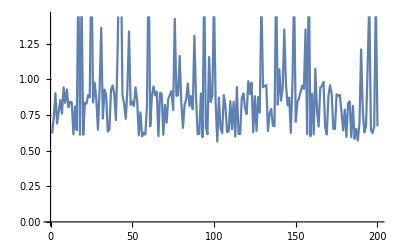

```mathematica
TimingData20 = Import["TimingDataComputation20.mx"];
ListLinePlot[TimingData20]
```

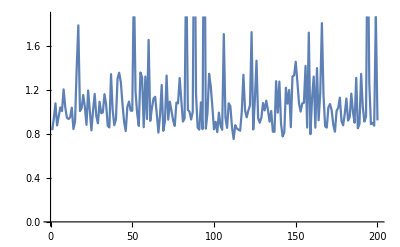

```mathematica
TimingData30 = Import["TimingDataComputation30.mx"];
ListLinePlot[TimingData30]
```

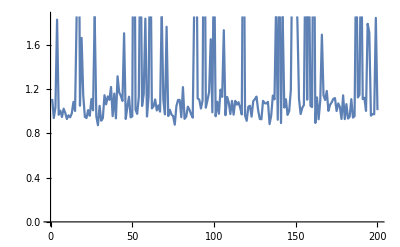

```mathematica
TimingData40 = Import["TimingDataComputation40.mx"];
ListLinePlot[TimingData40]
```

### Redo computations that seem off

```mathematica
numberTests = Dimensions[TimingData30][[1]];
i= 1;
While[i <= numberTests,
If[TimingData30[[i]] > 1.5,
TimingData30[[i]] = ComputationTime[ICData[[i]]];
Print[TimingData30[[i]]];
,
_];
i = i+ 1;
];
```

1.78993

0.833439

1.16538

1.30298

1.27195

2.21372

1.36019

1.6574

2.40477

3.13372

3.34156

1.34856

1.236

1.7098

0.829916

1.33981

1.72747

1.28124

1.27786

0.862461

1.32377

1.33353

1.27655

1.42013

1.72333

1.4001

1.80963

1.31148

2.73878

1.26215

1.89669

### Plotting the Distribution of Timing Data

Median (n = 20) = 0.840885

Interquartile Spread (n = 20) = 0.259035

Interquartile Spread / Median (n = 20) = 0.30805

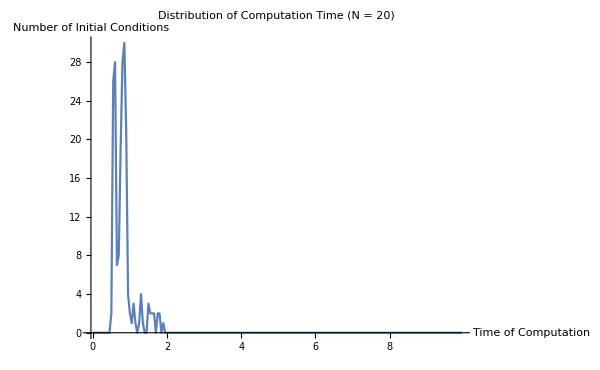

```mathematica
(* N = 20 *)

numberTests=Dimensions[TimingData20][[1]];
Tmax=10;
binLength=0.05;
epsilon=binLength/2;
numberBins=Tmax/binLength;
count20=ConstantArray[0,IntegerPart[numberBins]];
Print["Median (n = 20) = ",Median[TimingData20]];
Print["Interquartile Spread (n = 20) = ",InterquartileRange[TimingData20]];
Print["Interquartile Spread / Median (n = 20) = ",InterquartileRange[TimingData20] / Median[TimingData20]];
Table[Table[If[j*binLength-epsilon<=TimingData20[[i]]<=j*binLength+epsilon,count20[[j]]=count20[[j]]+1,_],{j,1,numberBins}];,{i,1,numberTests}];
xTicks=Table[{i,IntegerPart[(i-1)*binLength]},{i,1,IntegerPart[numberBins],IntegerPart[1/binLength]}];
ListLinePlot[count20,Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time (N = 20)"]
```

Median (n = 30) = 1.01112

Interquartile Spread (n = 30) = 0.250145

Interquartile Spread / Median (n = 30) = 0.247394

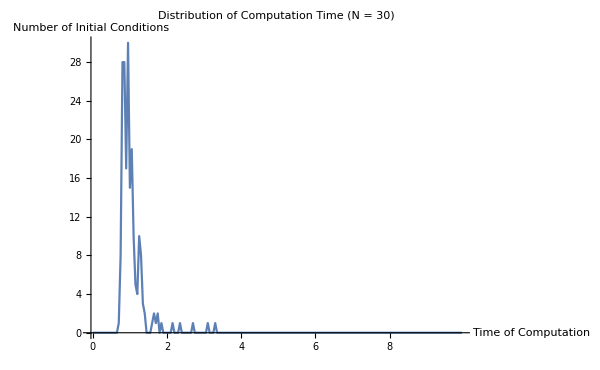

```mathematica
(* N = 30 *)

numberTests=Dimensions[TimingData30][[1]];
Tmax=10;
binLength=0.05;
epsilon=binLength/2;
numberBins=Tmax/binLength;
count30=ConstantArray[0,IntegerPart[numberBins]];
Print["Median (n = 30) = ",Median[TimingData30]];
Print["Interquartile Spread (n = 30) = ",InterquartileRange[TimingData30]];
Print["Interquartile Spread / Median (n = 30) = ",InterquartileRange[TimingData30] / Median[TimingData30]];
Table[Table[If[j*binLength-epsilon<=TimingData30[[i]]<=j*binLength+epsilon,count30[[j]]=count30[[j]]+1,_],{j,1,numberBins}];,{i,1,numberTests}];
xTicks=Table[{i,IntegerPart[(i-1)*binLength]},{i,1,IntegerPart[numberBins],IntegerPart[1/binLength]}];
ListLinePlot[count30,Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time (N = 30)"]
```

Median (n = 40) = 1.06005

Interquartile Spread (n = 40) = 0.171077

Interquartile Spread / Median (n = 40) = 0.235974

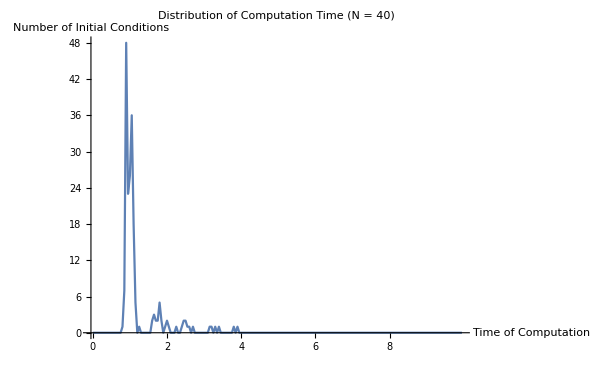

```mathematica
(* N = 40 *)

numberTests=Dimensions[TimingData40][[1]];
Tmax=10;
binLength=0.05;
epsilon=binLength/2;
numberBins=Tmax/binLength;
count40=ConstantArray[0,IntegerPart[numberBins]];
Print["Median (n = 40) = ",Median[TimingData40]];
Print["Interquartile Spread (n = 40) = ",InterquartileRange[TimingData40]];
Print["Interquartile Spread / Median (n = 40) = ",InterquartileRange[TimingData30] / Median[TimingData40]];
Table[Table[If[j*binLength-epsilon<=TimingData40[[i]]<=j*binLength+epsilon,count40[[j]]=count40[[j]]+1,_],{j,1,numberBins}];,{i,1,numberTests}];
xTicks=Table[{i,IntegerPart[(i-1)*binLength]},{i,1,IntegerPart[numberBins],IntegerPart[1/binLength]}];
ListLinePlot[count40,Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time (N = 40)"]
```

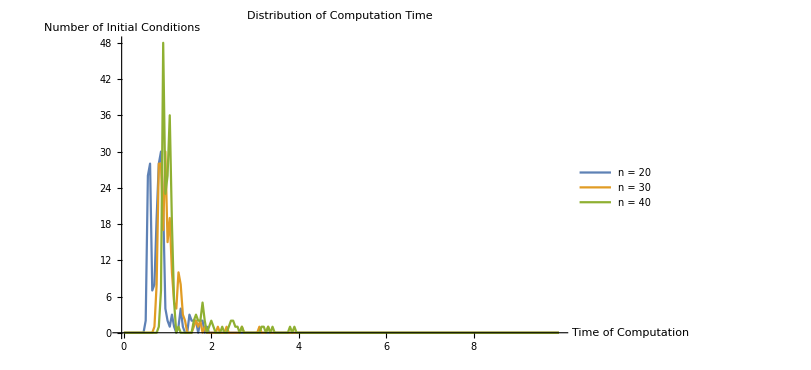

```mathematica
ListLinePlot[{count20,count30,count40},Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time ",PlotLegends->{"n = 20","n = 30","n = 40"}]
```